# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\quantum_chaotic_channels\MG files\Spin chain\All krauss operators

```mathematica
Get["D:\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
ClearAll[Superoperator](*nuevo*)
Superoperator[t_,ψ0E_,eigVals_,eigVecs_,L_]:=
	Module[{ψf,ρfSE(*SE final state*)},
		ψf=StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[#],ψ0E],eigVals,eigVecs]&/@{{0},{1}};
		ρfSE=Dyad[ψf[[#1]],ψf[[#2]]]&@@@Tuples[{1,2},2];
		Transpose[Flatten[MatrixPartialTrace[#,2,{2,2^(L-1)}]]&/@ρfSE]
];
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# ρ_s(t)

## LDoS

## Hamiltonian

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
L=4(*number of spins*);
{hx,hz,J}={1,0.5,ConstantArray[1,L-1]};
```

{0.792491,0.620727}

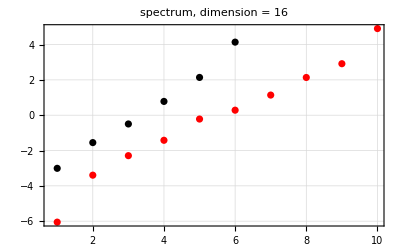

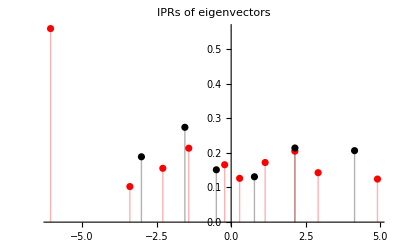

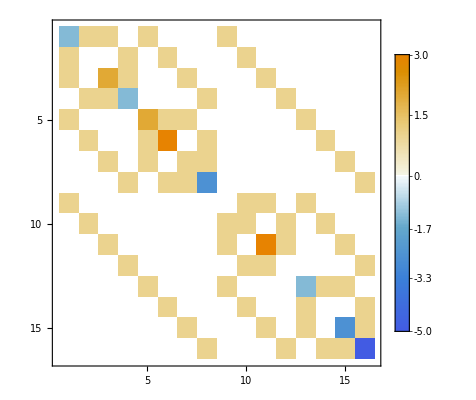

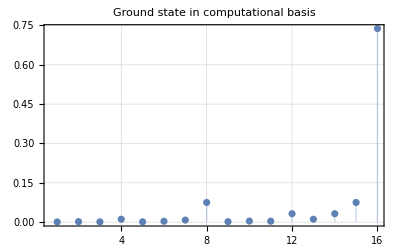

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
ListPlot[{EvenEigVals,OddEigVals},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Red,Black},ImageSize->400,PlotLabel->Style["spectrum, dimension = "<>ToString[2^L],25,Black]]
iprM=ParallelTable[Total[Quiet[Abs[i]^4]],{i,evenEigenVecs}];
iprm=ParallelTable[Total[Quiet[Abs[i]^4]],{i,OddEigVecs}];
ListPlot[{Transpose[{EvenEigVals,iprM}],Transpose[{OddEigVals,iprm}]},PlotRange->All,Filling->Axis,ImageSize->400,PlotStyle->{Red,Black},PlotLabel->Style["IPRs of eigenvectors",25,Black]]
MatrixPlot[H,PlotRange->All,PlotTheme->"Detailed"]
ListPlot[Abs[eigVecs[[1]]]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->400,PlotLabel->Style["Ground state in computational basis",25,Black]]
```

## Initial state all random

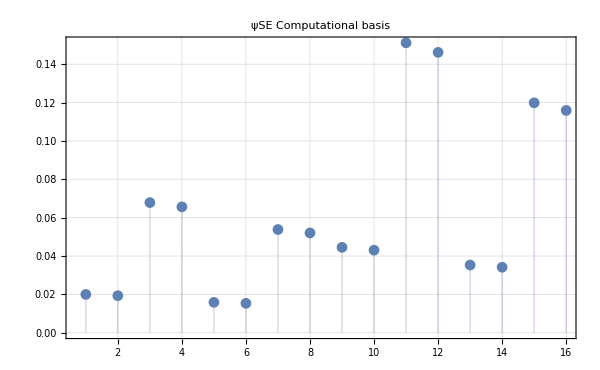
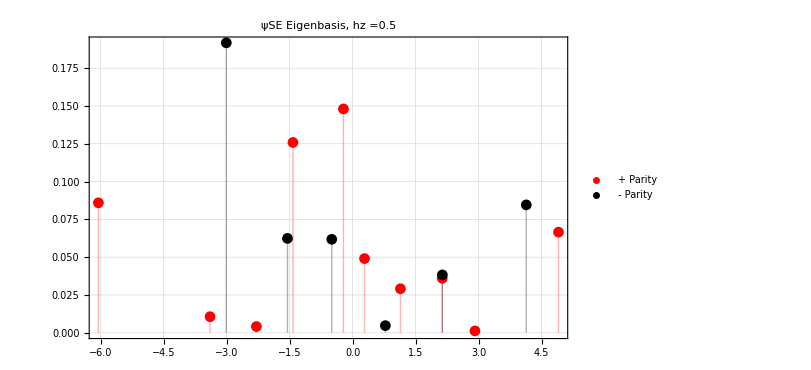

```mathematica
(*Set the seed SeedRandom[32371] and compute three initial states for the environment*)
SeedRandom[32371];
ψ0E=RandomChainProductState[L];
ψ0Espineven=Conjugate[evenEigenVecs].ψ0E;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0E;
plota=ListPlot[Abs[ψ0E]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 0random

```mathematica
SeedRandom[32371];
ψ0E=RandomChainProductState[L-1];
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E];
```

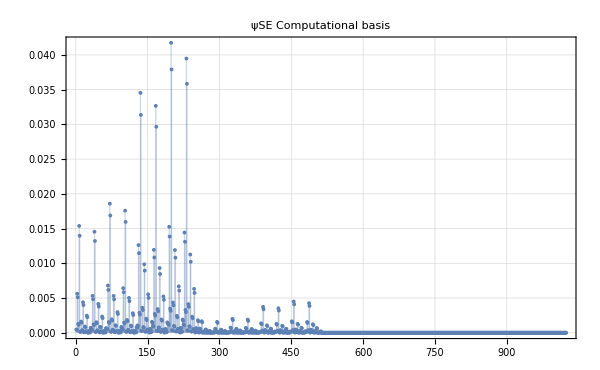
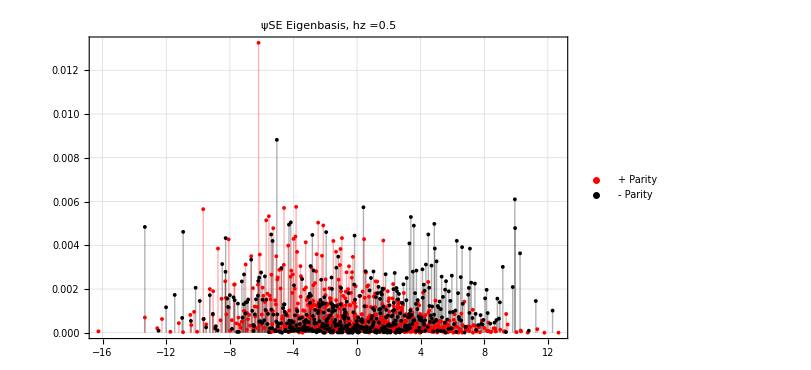

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 1random

```mathematica
SeedRandom[32371];
ψ0E=RandomChainProductState[L-1];
ψ0SE=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{1}],ψ0E];
```

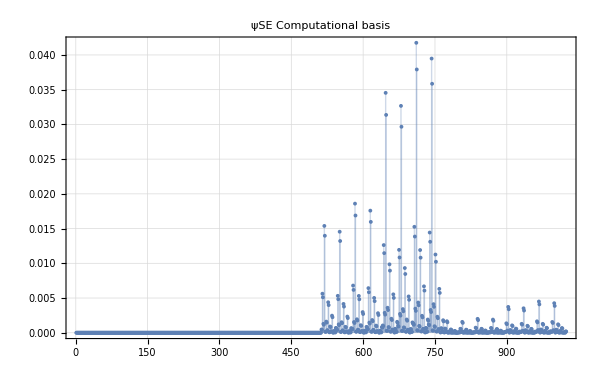
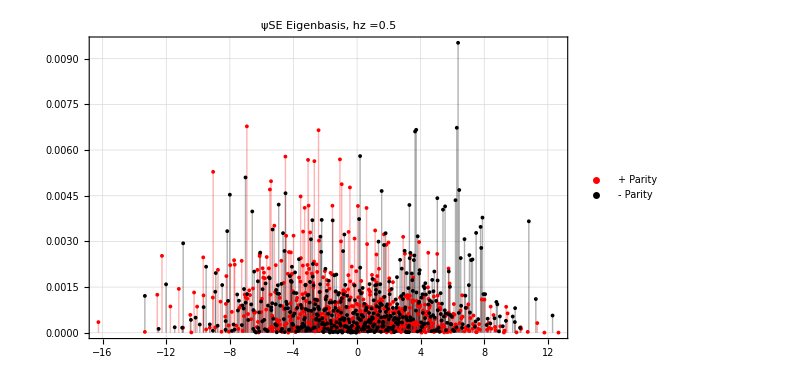

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 00..

```mathematica
Clear[ψ0SE];
ψ0SE=VectorFromKetInComputationalBasis[ConstantArray[0,L]];
```

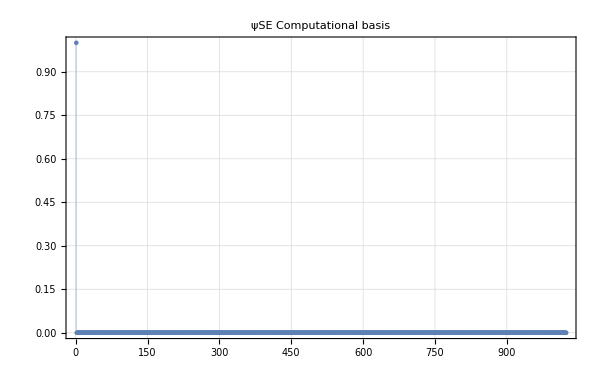
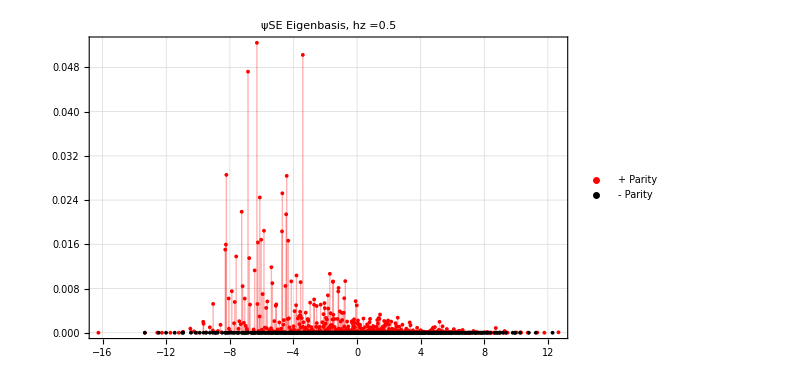

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state 11..

```mathematica
Clear[ψ0SE];
ψ0SE=VectorFromKetInComputationalBasis[ConstantArray[1,L]];
```

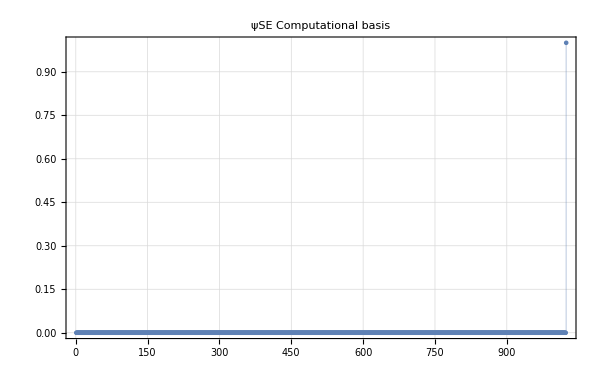
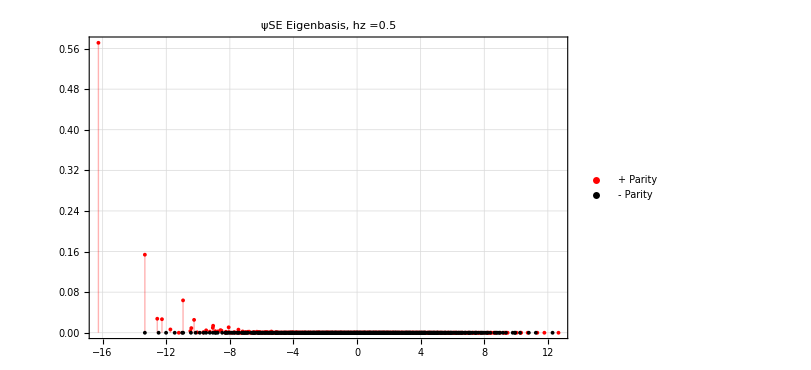

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## 0<=t<=50

```mathematica
?Superoperator
```

```mathematica
VectorFromKetInComputationalBasis[{0,0,0}]
```

{1,0,0,0,0,0,0,0}

```mathematica
KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],VectorFromKetInComputationalBasis[{0,0,0}]]//Dimensions
```

{16}

```mathematica
eigVals//Dimensions
```

{16}

```mathematica
eigVecs//Dimensions
```

{16,16}

```mathematica
Superoperator[0.5,VectorFromKetInComputationalBasis[{0,0,0}],eigVals,eigVecs,L]
```

{{0.776943+0. ⅈ,-0.0944758+0.399167 ⅈ,-0.0944758-0.399167 ⅈ,0.222992+0. ⅈ},{-0.0664675+0.391233 ⅈ,0.631918+0.284824 ⅈ,0.220128-0.0163478 ⅈ,0.0641265-0.390744 ⅈ},{-0.0664675-0.391233 ⅈ,0.220128+0.0163478 ⅈ,0.631918-0.284824 ⅈ,0.0641265+0.390744 ⅈ},{0.223057+0. ⅈ,0.0944758-0.399167 ⅈ,0.0944758+0.399167 ⅈ,0.777008+0. ⅈ}}

```mathematica
ψf=(StateEvolution[0.5,KroneckerVectorProduct[VectorFromKetInComputationalBasis[#1],VectorFromKetInComputationalBasis[{0,0,0}]],eigVals,eigVecs]&)/@{{0},{1}}
```

{{0.49621+0.396622 ⅈ,0.118233-0.312284 ⅈ,-0.0643637-0.285318 ⅈ,-0.165754-0.0388247 ⅈ,-0.0643637-0.285318 ⅈ,-0.134907+0.0824362 ⅈ,-0.158482+0.0623826 ⅈ,-0.00722797+0.0881635 ⅈ,0.118233-0.312284 ⅈ,-0.175113-0.00849615 ⅈ,-0.134907+0.0824362 ⅈ,0.00827569+0.0915461 ⅈ,-0.165754-0.0388247 ⅈ,0.00827569+0.0915461 ⅈ,-0.00722797+0.0881635 ⅈ,0.0400296+0.0227389 ⅈ},{0.118233-0.312284 ⅈ,-0.175114-0.00850342 ⅈ,-0.13438+0.0822683 ⅈ,0.00832763+0.0912588 ⅈ,-0.168846+0.0204568 ⅈ,0.0392026+0.083047 ⅈ,0.0239456+0.0861676 ⅈ,0.0459682+0.00763974 ⅈ,0.617008+0.0252319 ⅈ,-0.0877323-0.311999 ⅈ,-0.229314-0.194537 ⅈ,-0.160087+0.0685025 ⅈ,0.102697-0.311952 ⅈ,-0.177405-0.000594858 ⅈ,-0.151949-0.0312535 ⅈ,-0.0464567+0.0657714 ⅈ}}

```mathematica
ψf//Dimensions
```

{2,16}

```mathematica
ρfSE=(Dyad[ψf⟦#1⟧,ψf⟦#2⟧]&)@@@Tuples[{1,2},2];
ρfSE//Dimensions
```

{4,16,16}

```mathematica
Transpose[(Flatten[MatrixPartialTrace[#1,2,{2,2^(L-1)}]]&)/@ρfSE]//Dimensions
```

{4,4}

```mathematica
?Dyad
```

```mathematica
?StateEvolution
```

```mathematica
?MatrixPartialTrace
```

```mathematica
Tuples[{1,2},2]
```

{{1,1},{1,2},{2,1},{2,2}}

```mathematica
(*SeedRandom[32371];
ψ0SEa=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{0}],ψ0E];
ψ0SEb=KroneckerVectorProduct[VectorFromKetInComputationalBasis[{1}],ψ0E];
ψ0SEc=RandomChainProductState[L];
ψT={ψ0SEa,ψ0SEb,ψ0SEc};*)
```

```mathematica
(*Set the seed SeedRandom[32371] and compute three initial states for the environment*)
ψT=Table[RandomChainProductState[L-1],3];
```

```mathematica
ψT={VectorFromKetInComputationalBasis[ConstantArray[0,L-1]],VectorFromKetInComputationalBasis[ConstantArray[1,L-1]],RandomChainProductState[L-1]};
```

```mathematica
tf=1.;
```

```mathematica
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->400
]
];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];
AppendTo[listplots,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->500]];
,{i,3}]
```

```mathematica
Export["bloch_sphere_and_choi_eigenvalues_regular.avi",Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{1000,1200},Spacings->{50,50},Alignment->{Center,Bottom}],{t,0,tf,0.1}],"ImageResolution"->350,"FrameRate"->4,"VideoCompression"->"MPEG4"];
```

```mathematica
grids=Table[GraphicsGrid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],ImageSize->{1000,1200},Spacings->{50,50},Alignment->{Center,Bottom}],{t,0,tf,0.1}];
```

```mathematica
grids[[1]]
```

```mathematica
Export["chaotic_frame_"<>ToString[#]<>".png",grids[[#]],ImageResolution->200]&/@Range[Length[grids]];
```

```mathematica
Export["regular_frame_"<>ToString[#]<>".png",grids[[#]],ImageResolution->200]&/@Range[Length[grids]];
```

# All Kraus operators

First, let’s take the spin chain of size L = 4, so we have an enviroment of size 2^3 = 8. This will result in 8 Kraus operators and we know that we need at most 4 Canonical Kraus operators because the quantum channel we are interested evolves a single qubit density matrix.

For a fixed t  and some parameters in the Regular region

```mathematica
Clear[U];
U[t_]:=MatrixExp[-I H t];
```

```mathematica
t=1.5;
L=4;
{hx,hz,J}={1,3.0,ConstantArray[1,L-1]};
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

We chose the simplest state for the enviroment ψ0E = 000 and calculate the 8 Kraus operators

```mathematica
KrausOperators=Table[SparseArray[FromDigits[{r,#1,#2,#3},2]+1->1,2^L].U[t].SparseArray[FromDigits[{s,0,0,0},2]+1->1,2^L],{r,0,1},{s,0,1}]&@@@Tuples[{0,1},(L-1)];
```

```mathematica
(*Normalization condition*)
Chop@Sum[ConjugateTranspose[K].K,{K,KrausOperators}]
```

{{1.,0},{0,1.}}

```mathematica
KrausOperators//Dimensions
```

{8,2,2}

Then, the superoperator ϵ is the sum of the tensor product of all the Kraus operators

```mathematica
superoperatora=Sum[KroneckerProduct[i,Conjugate[i]],{i,KrausOperators}];
```

```mathematica
superoperatora//Dimensions
```

{4,4}

Let’s compare with the function SuperOperator

```mathematica
ψ0E=VectorFromKetInComputationalBasis[{0,0,0}];
```

```mathematica
superoperatorb=Superoperator[t,ψ0E,eigVals,eigVecs,L];
```

```mathematica
superoperatorb//Dimensions
```

{4,4}

```mathematica
superoperatora//MatrixForm
```

(0.962494+0. ⅈ | 0.0890478+0.14661 ⅈ | 0.0890478-0.14661 ⅈ | 0.0584791+0. ⅈ
0.0286946+0.165844 ⅈ | 0.75572-0.50152 ⅈ | 0.0331056+0.000124227 ⅈ | -0.0303817-0.127268 ⅈ
0.0286946-0.165844 ⅈ | 0.0331056-0.000124227 ⅈ | 0.75572+0.50152 ⅈ | -0.0303817+0.127268 ⅈ
0.0375064+0. ⅈ | -0.0890478-0.14661 ⅈ | -0.0890478+0.14661 ⅈ | 0.941521+0. ⅈ)

```mathematica
superoperatorb//MatrixForm
```

(0.962494+0. ⅈ | 0.0890478+0.14661 ⅈ | 0.0890478-0.14661 ⅈ | 0.0584791+0. ⅈ
0.0286946+0.165844 ⅈ | 0.75572-0.50152 ⅈ | 0.0331056+0.000124227 ⅈ | -0.0303817-0.127268 ⅈ
0.0286946-0.165844 ⅈ | 0.0331056-0.000124227 ⅈ | 0.75572+0.50152 ⅈ | -0.0303817+0.127268 ⅈ
0.0375064+0. ⅈ | -0.0890478-0.14661 ⅈ | -0.0890478+0.14661 ⅈ | 0.941521+0. ⅈ)

```mathematica
Eigenvalues[superoperatora]//Chop
Eigenvalues[superoperatorb]//Chop
```

{1.,0.97583,0.719812+0.583412 ⅈ,0.719812-0.583412 ⅈ}

{1.,0.97583,0.719812+0.583412 ⅈ,0.719812-0.583412 ⅈ}

```mathematica
choia=Reshuffle[superoperatora];
```

```mathematica
{choieigenval,choieigenvec}=Transpose[Sort[Transpose[Eigensystem[choia]]]];
```

```mathematica
choieigenval//Chop
```

{0.000442693,0.00533994,0.079161,1.91506}

```mathematica
Table[Chop[ConjugateTranspose[i].j],{i,choieigenvec},{j,choieigenvec}]//MatrixForm
```

(1. | 0 | 0 | 0
0 | 1. | 0 | 0
0 | 0 | 1. | 0
0 | 0 | 0 | 1.)

# Entanglement entropy of eigenvectors

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
L=8(*number of spins*);
{hx,hz,J}={1,0.5,ConstantArray[1,L-1]};
```

{0.569711,0.494574}

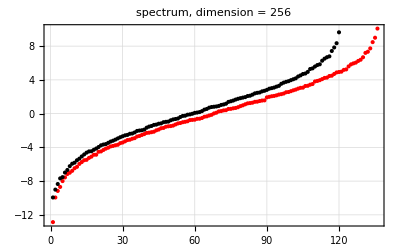

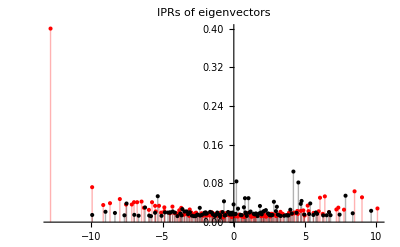

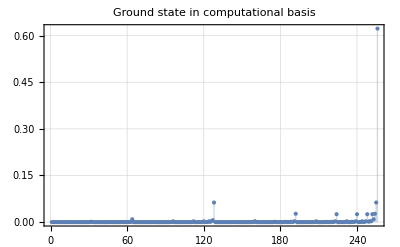

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
ListPlot[{EvenEigVals,OddEigVals},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Red,Black},ImageSize->400,PlotLabel->Style["spectrum, dimension = "<>ToString[2^L],25,Black]]
iprM=ParallelTable[Total[Quiet[Abs[i]^4]],{i,evenEigenVecs}];
iprm=ParallelTable[Total[Quiet[Abs[i]^4]],{i,OddEigVecs}];
ListPlot[{Transpose[{EvenEigVals,iprM}],Transpose[{OddEigVals,iprm}]},PlotRange->All,Filling->Axis,ImageSize->400,PlotStyle->{Red,Black},PlotLabel->Style["IPRs of eigenvectors",25,Black]]
ListPlot[Abs[eigVecs[[1]]]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->400,PlotLabel->Style["Ground state in computational basis",25,Black]]
```

```mathematica
rhos=ParallelTable[Dyad[i,i],{i,eigVecs}];
partialtrace=ParallelTable[MatrixPartialTrace[i,2,{2,2^(L-1)}],{i,rhos}];
entropies=ParallelTable[1-Tr[i^2],{i,rhos}];
```

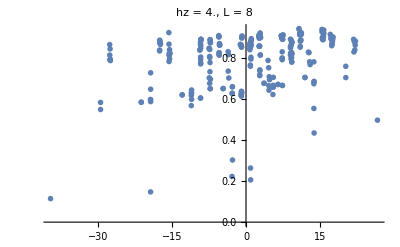

```mathematica
ListPlot[Transpose[{eigVals,entropies}],PlotRange->All,PlotMarkers->"OpenMarkers",PlotLabel->Style["hz = "<>ToString[hz]<>", L = "<>ToString[L],25,Black]]
```

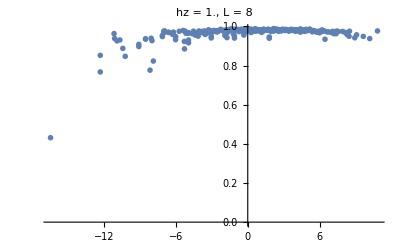

```mathematica
ListPlot[Transpose[{eigVals,entropies}],PlotRange->All,PlotMarkers->"OpenMarkers",PlotLabel->Style["hz = "<>ToString[hz]<>", L = "<>ToString[L],25,Black]]
```

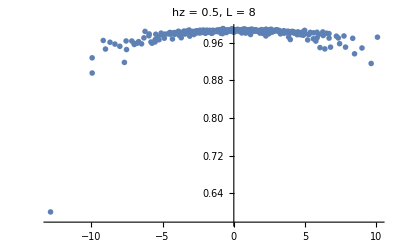

```mathematica
ListPlot[Transpose[{eigVals,entropies}],PlotRange->All,PlotMarkers->"OpenMarkers",PlotLabel->Style["hz = "<>ToString[hz]<>", L = "<>ToString[L],25,Black]]
```

# Eigenvalues of Choi

```mathematica
matrix={{1,2,3,4},{0,1,2,3},{4,0,1,2},{3,4,0,1}};
```

```mathematica
eigenvalues=Eigenvalues[matrix];
```

```mathematica
charPoly[λ_]:=Product[λ-eigenvalues[[i]],{i,1,Length[eigenvalues]}];
```

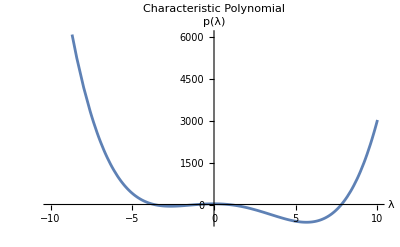

```mathematica
Plot[charPoly[λ],{λ,-10,10},PlotLabel->"Characteristic Polynomial",AxesLabel->{"λ","p(λ)"}]
```